```mathematica
Ln1=4;
Ln2=1;
com1=1;
com2=2;
```

P(l1<L1, l2< L2)

```mathematica
P1[l1_,l2_,c_,γ_]:=((l1+l2+c-1)!)/((c-1)!l1!l2!)*(1/(2+c*γ))^(l1+l2)((c*γ)/(2+c*γ))^c
```

P(l1<L1,l2=L2)

```mathematica
P2[l1_,L2_,c_,γ_]:=((l1+c-1)!)/(l1!(c-1)!)*(c*γ)^c/(c*γ+1)^(l1+c)-Sum[((l1+l2+c-1)!)/((c-1)!l1!l2!)*(c*γ)^c/(c*γ+2)^(l1+l2+c),{l2,0,L2-1}]
```

P(l1=L1,l2=L2). First term is all structures l1=(0-L1-1), l2=(0:L2). Second term is l1=L1, l2=L2-1. Note that L1 cannot be less than 1.

```mathematica
P3[L1_,L2_,c_,γ_]:=1-Sum[Sum[P1[l1,l2,c,γ],{l1,0,L1-1}],{l2,0,L2-1}]-Sum[P2[l1,L2,c,γ],{l1,0,L1-1}]-Sum[P2[l2,L1,c,γ],{l2,0,L2-1}]
```

```mathematica
T1=Evaluate@Table[P1[l1,l2,1,2],{l1,0,Ln1-1},{l2,0,Ln2-1}]
```

{{1/2},{1/8},{1/32},{1/128}}

```mathematica
T2=Evaluate@Table[P2[l1,Ln2,1,2],{l1,0,Ln1-1}]
```

{1/6,7/72,37/864,175/10368}

```mathematica
T3=Evaluate@Table[P2[l2,Ln1,1,2],{l2,0,Ln2-1}]
```

{1/384}

```mathematica
T4={T1,T2,T3,P3[Ln1,Ln2,1,2]}
```

{{{1/2},{1/8},{1/32},{1/128}},{1/6,7/72,37/864,175/10368},{1/384},101/10368}

```mathematica
T5=Flatten[T4]
```

{1/2,1/8,1/32,1/128,1/6,7/72,37/864,175/10368,1/384,101/10368}

```mathematica
Total[T5]
```

1

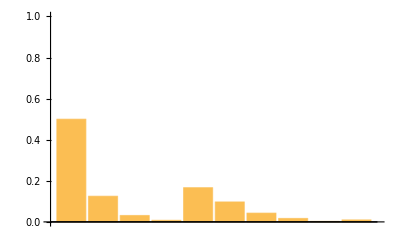

```mathematica
BarChart[T5, PlotRange->{0,1}]
```

```mathematica
T11=Evaluate@Table[P1[l1,l2,1,0.5],{l1,0,Ln1-1},{l2,0,Ln2-1}]
```

{{0.2},{0.08},{0.032},{0.0128}}

```mathematica
T12=Evaluate@Table[P2[l1,Ln2,1,0.5],{l1,0,Ln1-1}]
```

{0.133333,0.142222,0.116148,0.0859654}

```mathematica
T13=Evaluate@Table[P2[l2,Ln1,1,0.5],{l2,0,Ln2-1}]
```

{0.00853333}

```mathematica
T14={T11,T12,T13,P3[Ln1,Ln2,1,0.5]}
```

{{{0.2},{0.08},{0.032},{0.0128}},{0.133333,0.142222,0.116148,0.0859654},{0.00853333},0.188998}

```mathematica
T15=Flatten[T14]
```

{0.2,0.08,0.032,0.0128,0.133333,0.142222,0.116148,0.0859654,0.00853333,0.188998}

```mathematica
Total[T15]
```

1.

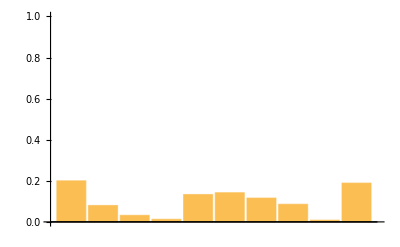

```mathematica
BarChart[T15, PlotRange->{0,1}]
```

```mathematica
T21=Evaluate@Table[P1[l1,l2,1,0.05],{l1,0,Ln1-1},{l2,0,Ln2-1}]
```

{{0.0243902},{0.0118977},{0.00580375},{0.0028311}}

```mathematica
T22=Evaluate@Table[P2[l1,Ln2,1,0.05],{l1,0,Ln1-1}]
```

{0.0232288,0.0334538,0.0373881,0.038304}

```mathematica
T23=Evaluate@Table[P2[l2,Ln1,1,0.05],{l2,0,Ln2-1}]
```

{0.00269628}

```mathematica
T24={T21,T22,T23,P3[Ln1,Ln2,1,0.05]}
```

{{{0.0243902},{0.0118977},{0.00580375},{0.0028311}},{0.0232288,0.0334538,0.0373881,0.038304},{0.00269628},0.820006}

```mathematica
T25=Flatten[T24]
```

{0.0243902,0.0118977,0.00580375,0.0028311,0.0232288,0.0334538,0.0373881,0.038304,0.00269628,0.820006}

```mathematica
Total[T15]
```

1.

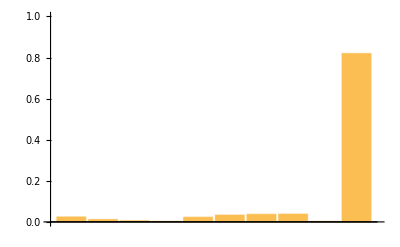

```mathematica
BarChart[T25,PlotRange->{0,1}]
```